## Section | Gram-Schmidt Orthogonalization (GSO)

Starting with an independent set of vectors or functions, {u_n}_(n=0,1,…), one can produce an orthonormal set using Gram-Schmidt orthogonalization (GSO),

v_0=u_0/(‖u_0‖), v_1=(u_1-⟨u_1,v_0⟩v_0)/(‖u_1-⟨u_1,v_0⟩v_0‖), v_2=(u_2-⟨u_2,v_0⟩v_0-⟨u_2,v_1⟩v_1)/(‖u_2-⟨u_2,v_0⟩v_0-⟨u_2,v_1⟩v_1‖), …,

where ⟨f,g⟩ is a suitable inner product and ‖f‖==√⟨f,f⟩ is the norm. Elements are orthonormal if ⟨v_i,v_j⟩==δ_(i,j).

GSO is built-in as Orthogonalize.

Starting with u_0={2,0,1}, u_1={3,5,7}, u_2={7,11,9}, use  Orthogonalize to produce the corresponding orthonormal set of vectors:

```mathematica
Orthogonalize[({{2, 0, 1}, {3, 5, 7}, {7, 11, 9}})]
```

(2/(√5) | 0 | 1/(√5)
-11/(√1230) | 5 √(5/246) | 11 √(2/615)
5/(√246) | 11/(√246) | -5 √(2/123))

Verify that these vectors are orthonormal:

```mathematica
%.Transpose[%]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

### Orthogonal Polynomials

LegendreP is a family of orthogonal polynomials with respect to the inner product

⟨f,g⟩:=∫_-1^1 f gⅆx.

Orthogonalize the polynomials x^k for k from zero through four to compute the first five (unnormalized) Legendre polynomials:

```mathematica
⟨f_,g_⟩:=∫_-1^1 f gⅆx
```

Hint: the inner product function here is A AngleBracket. [2 Marks]

```mathematica
Orthogonalize[x^Range[0,4],AngleBracket]//Factor
```

{1/(√2),√(3/2) x,1/2 √(5/2) (-1+3 x^2),1/2 √(7/2) x (-3+5 x^2),(3 (3-30 x^2+35 x^4))/(8 √2)}

Compare to the conventional Legendre polynomials:

```mathematica
LegendreP[Range[0,4],x]
```

{1,x,1/2 (-1+3 x^2),1/2 (-3 x+5 x^3),1/8 (3-30 x^2+35 x^4)}

For each k, e_k and kx differ by a factor of √(2/(2 k+1)):

```mathematica
Simplify[%/%%]
```

{√2,√(2/3),√(2/5),√(2/7),(√2)/3}

### Exercises

Construct a set of linearly independent polynomials, u_n(x), 0≤n≤4, such that u'_n(±1)==0. Hint: the constant function u_0(x)=1 satisfies u'_0(±1)==0. The polynomial (1-x^2) x^(n-1) vanishes at both ±1. [2 Marks]

Define u_0(x)=1 and u_n(x) by integrating the polynomial (1-x^2) x^(n-1):

```mathematica
Subscript[u, 0](x_)=1;
```

```mathematica
Subscript[u, n_](x_)=∫(1-x^2) x^(n-1)ⅆx
```

-x^n (x^2/(n+2)-1/n)

Verify that this set of polynomials satisfy u'_n(±1)==0:

```mathematica
{Subscript[u, 0]'(-1),Subscript[u, 0]'(1),Subscript[u, n]'(-1),Subscript[u, n]'(1)}//Simplify
```

{0,0,0,0}

The degree 1 polynomial a x+b has constant derivative a, which would require a=0 leading to a constant function.

The degree 2 (quadratic) polynomial a x^2+b x+c has derivative 2a x+b, which would require 2a+b==-2a+b==0⇒a==b==0.

Construct a set of linearly independent polynomials, u_n(x), 0≤n≤4:

```mathematica
us=Table[Subscript[u, n](x),{n,0,4}]
```

{1,-x (x^2/3-1),-x^2 (x^2/4-1/2),-x^3 (x^2/5-1/3),-x^4 (x^2/6-1/4)}

Aside: confirm that the set is linearly independent by computing the determinant of the matrix of successive derivatives and checking whether it vanishes in (-1,1):

```mathematica
NestList[f↦D[f, x],us,4]
```

(1 | -x (x^2/3-1) | -x^2 (x^2/4-1/2) | -x^3 (x^2/5-1/3) | -x^4 (x^2/6-1/4)
0 | 1-x^2 | -x^3/2-2 (x^2/4-1/2) x | -(2 x^4)/5-3 (x^2/5-1/3) x^2 | -x^5/3-4 (x^2/6-1/4) x^3
0 | -2 x | -(5 x^2)/2-2 (x^2/4-1/2) | -(14 x^3)/5-6 (x^2/5-1/3) x | -3 x^4-12 (x^2/6-1/4) x^2
0 | -2 | -6 x | -(54 x^2)/5-6 (x^2/5-1/3) | -16 x^3-24 (x^2/6-1/4) x
0 | 0 | -6 | -24 x | -56 x^2-24 (x^2/6-1/4))

```mathematica
Det[%]//Factor
```

12 (x-1)^4 (x+1)^4

Explain why polynomials of degree 1 or 2 cannot have zero derivative at both ±1. [1 Mark]

The determinant vanishes only when x=±1, so the basis is linearly independent.

Orthogonalize the u_n(x) with respect to the inner product ⟨f,g⟩:=∫_-1^1 f gⅆx to obtain an orthonormal set polynomials over the interval [-1,1]. Hint: the inner product function here is AngleBracket. [2 Marks]

Define the inner product:

```mathematica
⟨f_,g_⟩:=∫_-1^1 f gⅆx;
```

Construct the corresponding orthonormal set of polynomials over the interval [-1,1]:

```mathematica
vs=Orthogonalize[us,AngleBracket]//Factor
```

{1/(√2),-1/2 √(35/34) x (x^2-3),-1/8 √(7/6) (15 x^4-30 x^2+7),-1/16 √(77/221) x (153 x^4-290 x^2+105),-1/32 √(65/159) (693 x^6-1365 x^4+651 x^2-43)}

Plot these polynomials. How many nodes does each u_n(x) have in the interval [-1,1]? [2 Marks]

Add a Tooltip to identify u_n(x) using MapIndexed:

```mathematica
MapIndexed[{f,n}↦Tooltip[f,First[n]-1],vs]
```

{1/(√2),-1/2 √(35/34) x (x^2-3),-1/8 √(7/6) (15 x^4-30 x^2+7),-1/16 √(77/221) x (153 x^4-290 x^2+105),-1/32 √(65/159) (693 x^6-1365 x^4+651 x^2-43)}

Plot this orthonormal set of polynomials over [-1,1]:

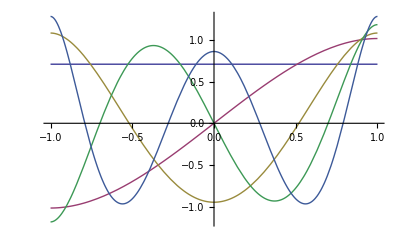

```mathematica
Plot[%,{x,-1,1}]
```

Alternatively, use TabView:

```mathematica
TabView@Table[n->Plot[vs⟦n+1⟧,{x,-1,1}],{n,0,4}]
```

12345

Clearly u_n(x) has n nodes in the interval [-1,1].